```mathematica
s[1,1]
```

0.00188385

```mathematica
s[1,1]*kappa
```

0.000753542

```mathematica
s[ww,w]*ww*kappa*ww^(-lambda)/.{ww->1,w->1}
```

0.000753542

```mathematica
s[ww,w]*ww*kappa*ww^(-lambda)/.{ww->1,w->1}
```

0.000753542

```mathematica
kappa=0.4;
q=0.8;
n=2/3;
beta=100;
sigma=1.3;
gamma=600.4424;
fbar=0.5;
k=0;
we=0.001;
eta=1/4;
u=10;
matsize=19.35659;
alpha=0.19
```

0.19

```mathematica
lambda
phi[1]
```

2.23333

3.99705

```mathematica
lambda=2+q-n
s[ww_,w_]:=Exp[-((Log[(beta*ww/w)])^2)/(2*sigma*sigma)]
phi[w_]:=NIntegrate[s[ww,w]*ww*kappa*ww^(-lambda),{ww,0,Infinity}]
Ee[w_]:=gamma*(w^q)*phi[w]
hFun[w_]:=((Ee[w]/fbar)-Ee[w])/(w^n)
alphaE=Sqrt[2*Pi]*gamma*sigma*(beta^(lambda-2))*Exp[((lambda-2)^2)*(sigma^2)/2]
Ee2[w_]:=alphaE*kappa*w^n
hval =((alphaE*kappa/fbar)-alphaE*kappa)
hbar=hval*fbar*alpha-k
maxsize=matsize/eta
psi[w_,ws_]:=((1+(w/ws)^(-u))^(-1))*((ws/w)^(n-1))*eta^(1-n)
Steppsi[w_,ws_]:=Piecewise[{{0,w<matsize},{((ws/w)^(n-1))*eta^(1-n),w≥matsize}}]

growthrate[w_]:=(hbar*w^n)*(1-psi[w,matsize])
growthrateStepPsi[w_]:=(hbar*w^n)*(1-Steppsi[w,matsize])

mort[w_]:=NIntegrate[(1-fbar)*kappa*(ww^(-lambda))*s[w,ww]*gamma*ww^q,{ww,0,Infinity}]
alphaP=(1-fbar)*Sqrt[2*Pi]*kappa*gamma*sigma*(beta^(1+q-lambda))*Exp[sigma*sigma*((1+q-lambda)^2)/2]
mort2[w_]:=alphaP*w^(n-1)
N1[w_]:=Exp[-NIntegrate[mort2[ww]/growthrate[ww],{ww,we,w}]]/growthrate[w]
N1tamed[w_]:=Piecewise[{{N1[w],we<=w<matsize/eta},{0,w≤we},{0,matsize/eta≤w}}]
kappaout=NIntegrate[matsize*N1tamed[y]*(y^(lambda+1))*y^(-2),{y,0,Infinity}]
HH=kappa/kappaout
Nsol[w_]:=HH*N1tamed[w]
LHS=Nsol[we]*growthrate[we]
RHSS=
NIntegrate[Nsol[W]*psi[W,matsize]*hbar*W^n,{W,0,Infinity}]/(2*we)
reproeff=LHS/RHSS
```

2.13333

3670.25

1468.1

139.469

77.4264

92.6069

NIntegrate::nlim: ww = y is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.00123406}. NIntegrate obtained 0.0688393 and 4.26672×10^-7 for the integral and error estimates.

0.0688393

5.81063

5.81063

NIntegrate::nlim: ww = W is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in W near {W} = {68.1055}. NIntegrate obtained 0.294059 and 0.000157415 for the integral and error estimates.

147.029

0.0395202

```mathematica
s[ww_,w_]:=Exp[-((Log[(beta*ww/w)])^2)/(2*sigma*sigma)]
phi[w_]:=NIntegrate[s[ww,w]*ww*kappa*ww^(-lambda),{ww,0,Infinity}]
Ee[w_]:=gamma*(w^q)*phi[w]
hFun[w_]:=((Ee[w]/fbar)-Ee[w])/(w^n)
Ee2[w_]:=alphaE*kappa*w^n
psi[w_,ws_]:=((1+(w/ws)^(-u))^(-1))*((ws/w)^(n-1))*eta^(1-n)
Steppsi[w_,ws_]:=Piecewise[{{0,w<matsize},{((ws/w)^(n-1))*eta^(1-n),w≥matsize}}]

growthrate[w_]:=(hbar*w^n)*(1-psi[w,matsize])
growthrateStepPsi[w_]:=(hbar*w^n)*(1-Steppsi[w,matsize])

mort[w_]:=NIntegrate[(1-fbar)*kappa*(ww^(-lambda))*s[w,ww]*gamma*ww^q,{ww,0,Infinity}]
mort2[w_]:=alphaP*w^(n-1)
N1[w_]:=Exp[-NIntegrate[mort2[ww]/growthrate[ww],{ww,we,w}]]/growthrate[w]
N1tamed[w_]:=Piecewise[{{N1[w],we<=w<matsize/eta},{0,w≤we},{0,matsize/eta≤w}}]
Nsol[w_]:=HH*N1tamed[w]
```

```mathematica
getreproeff[kappa_,q_,n_,beta_,sigma_,gamma_,fbar_,k_,we_,eta_,u_,matsize_,alpha_]:=
Module[{lambda=2+q-n},
Module[{alphaE=Sqrt[2*Pi]*gamma*sigma*(beta^(lambda-2))*Exp[((lambda-2)^2)*(sigma^2)/2]},
Module[{hval =((alphaE*kappa/fbar)-alphaE*kappa),maxsize=matsize/eta},
Module[{hbar=hval*fbar*alpha-k},
Module[{alphaP=(1-fbar)*Sqrt[2*Pi]*kappa*gamma*sigma*(beta^(1+q-lambda))*Exp[sigma*sigma*((1+q-lambda)^2)/2]},
Module[{kappaout=NIntegrate[matsize*N1tamed[y]*(y^(lambda+1))*y^(-2),{y,0,Infinity}]},
Module[{HH=kappa/kappaout},
Module[{LHS=Nsol[we]*growthrate[we],RHSS=
NIntegrate[Nsol[W]*psi[W,matsize]*hbar*W^n,{W,0,Infinity}]/(2*we)},
LHS/RHSS
]]]]]]]]
```

```mathematica
getreproeff[kappa_,q_,n_,beta_,sigma_,gamma_,fbar_,k_,we_,eta_,u_,matsize_,alpha_]:=(
lambda=2+q-n
s[ww_,w_]:=Exp[-((Log[(beta*ww/w)])^2)/(2*sigma*sigma)]
phi[w_]:=NIntegrate[s[ww,w]*ww*kappa*ww^(-lambda),{ww,0,Infinity}]
Ee[w_]:=gamma*(w^q)*phi[w]
hFun[w_]:=((Ee[w]/fbar)-Ee[w])/(w^n)
alphaE=Sqrt[2*Pi]*gamma*sigma*(beta^(lambda-2))*Exp[((lambda-2)^2)*(sigma^2)/2]
Ee2[w_]:=alphaE*kappa*w^n
hval =((alphaE*kappa/fbar)-alphaE*kappa)
hbar=hval*fbar*alpha-k
maxsize=matsize/eta
psi[w_,ws_]:=((1+(w/ws)^(-u))^(-1))*((ws/w)^(n-1))*eta^(1-n)
Steppsi[w_,ws_]:=Piecewise[{{0,w<matsize},{((ws/w)^(n-1))*eta^(1-n),w≥matsize}}]

growthrate[w_]:=(hbar*w^n)*(1-psi[w,matsize])
growthrateStepPsi[w_]:=(hbar*w^n)*(1-Steppsi[w,matsize])

mort[w_]:=NIntegrate[(1-fbar)*kappa*(ww^(-lambda))*s[w,ww]*gamma*ww^q,{ww,0,Infinity}]
alphaP=(1-fbar)*Sqrt[2*Pi]*kappa*gamma*sigma*(beta^(1+q-lambda))*Exp[sigma*sigma*((1+q-lambda)^2)/2]
mort2[w_]:=alphaP*w^(n-1)
N1[w_]:=Exp[-NIntegrate[mort2[ww]/growthrate[ww],{ww,we,w}]]/growthrate[w]
N1tamed[w_]:=Piecewise[{{N1[w],we<=w<matsize/eta},{0,w≤we},{0,matsize/eta≤w}}]
kappaout=NIntegrate[matsize*N1tamed[y]*(y^(lambda+1))*y^(-2),{y,0,Infinity}]
HH=kappa/kappaout
Nsol[w_]:=HH*N1tamed[w]
LHS=Nsol[we]*growthrate[we]
RHSS=
NIntegrate[Nsol[W]*psi[W,matsize]*hbar*W^n,{W,0,Infinity}]/(2*we)
reproeff=LHS/RHSS)
```

```mathematica
kappa2=0.4;
q2=0.8;
n2=2/3;
beta2=100;
sigma2=1.3;
gamma2=600.4424;
fbar2=0.5;
k2=0;
we2=0.001;
eta2=1/4;
u2=10;
matsize2=19.35659;
alpha2=0.19
```

0.19

```mathematica
getreproeff[kappa2,q2,n2,beta2,sigma2,gamma2,fbar2,k2,we2,eta2,u2,matsize2,alpha2]
```

NIntegrate::nlim: ww = we is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand 19.3566\ y^1.13333\ (TagBox[GridBox[{{"{", GridBox[{{ⅇ^-NIntegrate[« 2 »]\ y^-n/hbar\ (1 + Times[« 4 »]), we ≤ y < matsize/eta}, {"0", TagBox["True", "PiecewiseDefault", Rule[AutoDelete, True]]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 1.2, ColumnWidths -> Automatic, AllowedDimensions -> {2, Automatic}, Selectable -> True, Editable -> True]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 0.5, ColumnWidths -> Automatic], "Piecewise", Rule[SyntaxForm, Equal], Rule[SelectWithContents, True], Rule[Selectable, False], Rule[Editable, False], Rule[DeleteWithContents, True]]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate::inumr: The integrand 139.469\ 19.3566^-1 + n\ eta^1 - n\ HH\ (1/W)^n\ W^5/3\ (TagBox[GridBox[{{"{", GridBox[{{ⅇ^-NIntegrate[« 2 »]\ W^-n/hbar\ (1 + Times[« 4 »]), we ≤ W < matsize/eta}, {"0", TagBox["True", "PiecewiseDefault", Rule[AutoDelete, True]]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 1.2, ColumnWidths -> Automatic, AllowedDimensions -> {2, Automatic}, Selectable -> True, Editable -> True]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 0.5, ColumnWidths -> Automatic], "Piecewise", Rule[SyntaxForm, Equal], Rule[SelectWithContents, True], Rule[Selectable, False], Rule[Editable, False], Rule[DeleteWithContents, True]])/1 + 0.051662^-u\ W^-u has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

(0.002 0.001^n hbar HH (1-(1000.^(-1+n) eta^(1-n) matsize^(-1+n))/(1+0.001^-u (1/matsize)^-u)) (Piecewise[{{(0.001^-n ⅇ^(-NIntegrate[mort2[ww]/growthrate[ww],{ww,we,0.001}]))/(hbar (1-(1000.^(-1+n) eta^(1-n) matsize^(-1+n))/(1+0.001^-u (1/matsize)^-u))), we≤0.001<matsize/eta}, {0, True}}]))/NIntegrate[Nsol[W] psi[W,19.3566] hbar$599 W^(2/3),{W,0,∞}]

```mathematica
getreproeff[kappa,q,n,beta,sigma,gamma,fbar,k,we,eta,u,matsize,alpha]
```

NIntegrate::nlim: ww = y is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.00123406}. NIntegrate obtained 0.0688393 and 4.26672×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in W near {W} = {68.1055}. NIntegrate obtained 0.294059 and 0.000157415 for the integral and error estimates.

0.0395202

```mathematica
getreproeff[kappa,q,n,beta,sigma,gamma,fbar,k,we,eta,u,matsize,2*alpha]
```

NIntegrate::nlim: ww = y is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.00123406}. NIntegrate obtained 0.0688393 and 4.26672×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in W near {W} = {68.1055}. NIntegrate obtained 0.294059 and 0.000157415 for the integral and error estimates.

0.0395202

```mathematica
{kappa,q,n,beta,sigma,gamma,fbar,k,we,eta,u,matsize,alpha}
```

```mathematica
{0.4;
q=0.8;
n=2/3;
beta=100;
sigma=1.3;
gamma=600.4424;
fbar=0.5;
k=0;
we=0.001;
eta=1/4;
u=10;
matsize=19.35659;
alpha=0.19
```

```mathematica
myfun[z_]:=(a=1;b=2;,a+b*z)
```

```mathematica
myfun[2]
```

myfun[2]

2.13333

3670.25

1468.1

139.469

77.4264

92.6069

NIntegrate::nlim: ww = y is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.00123406}. NIntegrate obtained 0.0688393 and 4.26672×10^-7 for the integral and error estimates.

0.0688393

5.81063

5.81063

NIntegrate::nlim: ww = W is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in W near {W} = {68.1055}. NIntegrate obtained 0.294059 and 0.000157415 for the integral and error estimates.

147.029

0.0395202

```mathematica
reproeff
```

0.0395202

```mathematica
HH=kappa/kappaout
```

5.81063

```mathematica
Nsol[w_]:=HH*N1tamed[w]
```

```mathematica
LHS=Nsol[we]*growthrate[we]
```

5.81063

```mathematica
N1[we]
```

0.717003

```mathematica
NIntegrate[Nsol[ww]*psi[ww,matsize]*hbar*ww^n,{ww,0,10^5}]
```

```mathematica
RHSS=
NIntegrate[Nsol[ww]*psi[ww,matsize]*hbar*ww^n,{ww,1,2}]
```

NIntegrate::nlim: ww = ww is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand 190.14\ (1/ww)^2/3\ ww^5/3\ (TagBox[GridBox[{{"{", GridBox[{{0.00717003\ ⅇ^-NIntegrate[« 2 »]/(1 + Times[« 3 »])\ ww^2/3, 0.001 ≤ ww < 77.4264}, {"0", TagBox["True", "PiecewiseDefault", Rule[AutoDelete, True]]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 1.2, ColumnWidths -> Automatic, AllowedDimensions -> {2, Automatic}, Selectable -> True, Editable -> True]}}, ColumnAlignments -> {Left}, ColumnSpacings -> 0.5, ColumnWidths -> Automatic], "Piecewise", Rule[SyntaxForm, Equal], Rule[SelectWithContents, True], Rule[Selectable, False], Rule[Editable, False], Rule[DeleteWithContents, True]])/1 + 7.38395×10^12/ww^10 has evaluated to non-numerical values for all sampling points in the region with boundaries {{1, 2}}.

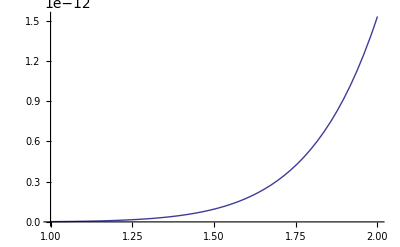

```mathematica
Plot[Nsol[ww]*psi[ww,matsize]*hbar*ww^n,{ww,1,2}]
```

```mathematica
NIntegrate[Nsol[www]*psi[www,matsize]*hbar*www^n,{www,1,2}]
```

NIntegrate::nlim: ww = www is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

2.86886×10^-13

```mathematica
LHS<-nvgood[1]*growth_rate[1]
RHSS<-sum(((nvgood*psi*hbar*wvec^nval)[1:(length(wvec)-1)])*(wvec[2:length(wvec)]-wvec[1:(length(wvec)-1)]))/(2*egg_size)
repro_efff<-LHS/RHSS
```

2.13333

3670.25

1468.1

139.469

77.4264

92.6069

```mathematica
N1tamed[3]
```

Piecewise::pairs: The first argument {{0.0000169298, True}, 0} of Piecewise is not a list of pairs.

Piecewise[{{N1[3],we<3<matsize/eta},0}]

NIntegrate::nlim: ww = w is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

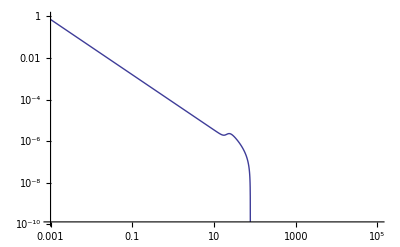

```mathematica
LogLogPlot[N1tamed[w],{w,we,10^5}]
```

```mathematica
kappaout=NIntegrate[matsize*N1tamed[y]*(y^(lambda+1))*y^(-2),{y,0,Infinity}]
```

NIntegrate::nlim: ww = y is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.00123406}. NIntegrate obtained 0.0688393 and 4.26672×10^-7 for the integral and error estimates.

0.0688393

```mathematica
LogLogPlot[N1tamed[w],{w,we,10^5}]
```

NIntegrate::nlim: ww = w is not a valid limit of integration.

Piecewise::pairs: The first argument {{0.00717003\ ⅇ^-NIntegrate[mort2[« 1 »]\ Power[« 2 »], {ww, we, w}]/(1 - 0.234623/Plus[« 2 »]\ Power[« 2 »]^1/3)\ w^2/3, 0.001 < w < 77.4264}, 0} of Piecewise is not a list of pairs.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Join::heads: Heads Hold and Table at positions 1 and 2 are expected to be the same.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

Join::heads: Heads Hold and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ww near {ww} = {-0.000388518}. NIntegrate obtained 10.2554  - 8.326×10^-7\ ⅈ
 and 4.90824 for the integral and error estimates.

Piecewise::pairs: The first argument {{-3.47624×10^-8 - 6.02086×10^-8\ ⅈ, False}, 0} of Piecewise is not a list of pairs.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ww near {ww} = {-0.000388518}. NIntegrate obtained 10.2554  - 8.326×10^-7\ ⅈ
 and 4.90824 for the integral and error estimates.

Piecewise::pairs: The first argument {{-3.47624×10^-8 - 6.02086×10^-8\ ⅈ, False}, 0.} of Piecewise is not a list of pairs.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ww near {ww} = {-0.000312959}. NIntegrate obtained 2.8475  - 4.66979×10^-7\ ⅈ
 and 3.59817 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

Piecewise::pairs: The first argument {{-0.0000594984 - 0.000103053\ ⅈ, False}, 0} of Piecewise is not a list of pairs.

General::stop: Further output of Piecewise :: pairs will be suppressed during this calculation.

-Graphics-

```mathematica
Piecewise[{{x^2,x<0},{x,x>0}}]
```

```mathematica
matsize*N1[y]*(y^(lambda+1))N1[y]*y^(-2)
```

2.13333

3670.25

1468.1

139.469

77.4264

92.6069

```mathematica
N1[0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ww near {ww} = {1.22413×10^-228}. NIntegrate obtained -127229. and 106490. for the integral and error estimates.

Power::infy: Infinite expression 1/0.^10 encountered.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

ComplexInfinity

```mathematica
kappaintegrand<-matsize*y^((lambda+1)*(1))*n1^(1)*y^(-2)
LL<-length(wvec)-1
kappaoutput<-sum(kappaintegrand[1:LL]*(wvec[2:(LL+1)]-wvec[1:LL]))
```

```mathematica
growthrate[we]
```

1.39469

```mathematica
N1[we]
```

0.717003

```mathematica
N1[24.33404]
```

2.26494×10^-6

NIntegrate::nlim: ww = w is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ww near {ww} = {-0.000388518}. NIntegrate obtained 10.2554  - 8.326×10^-7\ ⅈ
 and 4.90824 for the integral and error estimates.

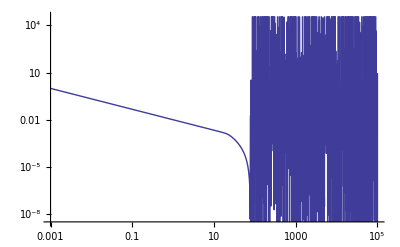

```mathematica
LogLogPlot[N1[w],{w,we,10^5}]
```

NIntegrate::nlim: ww = w is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ww near {ww} = {-0.000388547}. NIntegrate obtained 10.2337  - 8.32782×10^-7\ ⅈ
 and 4.88875 for the integral and error estimates.

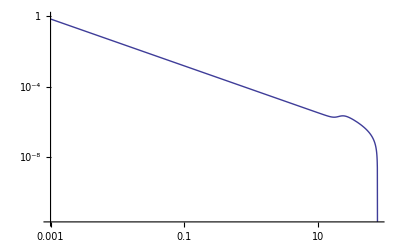

```mathematica
LogLogPlot[N1[w],{w,we,matsize/eta}]
```

NIntegrate::nlim: ww = w is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ww near {ww} = {-0.000388548}. NIntegrate obtained 10.2331  - 8.32788×10^-7\ ⅈ
 and 4.88815 for the integral and error estimates.

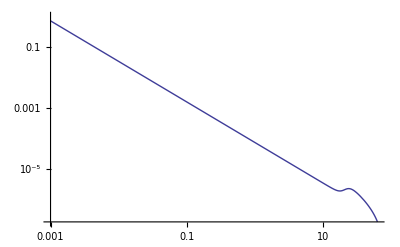

```mathematica
LogLogPlot[N1[w],{w,we,61.99335}]
```

```mathematica
N1[we]
```

1.

```mathematica
Integrate[(mu0*ww^(n-1))/(g0*(ww^n)*Steppsi[ww,ws]),ww]
```

Piecewise[{{ComplexInfinity, matsize-ww>0}, {(eta^(-1+n) mu0 ws (ws/ww)^-n)/(g0 (-1+n) ww), True}}]

```mathematica
ans=Exp[-Integrate[mort2[ww]/growthrateStepPsi[ww],{ww,we,w}]]/growthrate
```

Integrate::pwrl: Unable to prove that integration limits {w, we} are real. Adding assumptions may help.

1/growthrate ⅇ^(-∫_we^w (beta^(-1+n) ⅇ^(1/2 (-1+n)^2 sigma^2) (1-fbar) gamma kappa √(2 π) sigma)/((-k+alpha fbar (-beta^(-n+q) ⅇ^(1/2 (-n+q)^2 sigma^2) gamma kappa √(2 π) sigma+(beta^(-n+q) ⅇ^(1/2 (-n+q)^2 sigma^2) gamma kappa √(2 π) sigma)/fbar)) ww (1-(Piecewise[{{0, ww<matsize}, {eta^(1-n) (matsize/ww)^(-1+n), ww≥matsize}, {0, True}}])))ⅆww)

```mathematica
Plot[Piecewise[{{x^2,x<0},{x,x>0}}],{x,-2,2}]
```

2-n+q

beta^(-n+q) ⅇ^(1/2 (-n+q)^2 sigma^2) gamma √(2 π) sigma

-beta^(-n+q) ⅇ^(1/2 (-n+q)^2 sigma^2) gamma kappa √(2 π) sigma+(beta^(-n+q) ⅇ^(1/2 (-n+q)^2 sigma^2) gamma kappa √(2 π) sigma)/fbar

-k+alpha fbar (-beta^(-n+q) ⅇ^(1/2 (-n+q)^2 sigma^2) gamma kappa √(2 π) sigma+(beta^(-n+q) ⅇ^(1/2 (-n+q)^2 sigma^2) gamma kappa √(2 π) sigma)/fbar)

matsize/eta

beta^(-1+n) ⅇ^(1/2 (-1+n)^2 sigma^2) (1-fbar) gamma kappa √(2 π) sigma

```mathematica
Integrate[mort2[w]/growthrate[w],w]
```

(beta^(-1+n) ⅇ^(1/2 (-1+n)^2 sigma^2) (1-fbar) gamma kappa √(2 π) sigma ∫1/(w (1-(eta^(1-n) (matsize/w)^(-1+n))/(1+(w/matsize)^-u)))ⅆw)/(-k+alpha fbar (-beta^(-n+q) ⅇ^(1/2 (-n+q)^2 sigma^2) gamma kappa √(2 π) sigma+(beta^(-n+q) ⅇ^(1/2 (-n+q)^2 sigma^2) gamma kappa √(2 π) sigma)/fbar))

```mathematica
Integrate[mort2[w]/growthrateStepPsi[w],w]
```

Piecewise[{{(beta^(-1+2 n) ⅇ^(1/2 (-1+n)^2 sigma^2) (-1+fbar) gamma kappa √(2 π) sigma Log[w])/(beta^n k+alpha beta^q ⅇ^(1/2 (n-q)^2 sigma^2) (-1+fbar) gamma kappa √(2 π) sigma), matsize-w>0}, {(beta^(-1+2 n) ⅇ^(1/2 (-1+n)^2 sigma^2) (-1+fbar) gamma kappa √(2 π) sigma ((-1+n) Log[w]+Log[-eta^n matsize+eta (matsize/w)^n w]))/((-1+n) (beta^n k+alpha beta^q ⅇ^(1/2 (n-q)^2 sigma^2) (-1+fbar) gamma kappa √(2 π) sigma)), True}}]

```mathematica
anss=Integrate[mort2[w]/growthrateStepPsi[w],w]
```

Piecewise[{{(beta^(-1+2 n) ⅇ^(1/2 (-1+n)^2 sigma^2) (-1+fbar) gamma kappa √(2 π) sigma Log[w])/(beta^n k+alpha beta^q ⅇ^(1/2 (n-q)^2 sigma^2) (-1+fbar) gamma kappa √(2 π) sigma), matsize-w>0}, {(beta^(-1+2 n) ⅇ^(1/2 (-1+n)^2 sigma^2) (-1+fbar) gamma kappa √(2 π) sigma ((-1+n) Log[w]+Log[-eta^n matsize+eta (matsize/w)^n w]))/((-1+n) (beta^n k+alpha beta^q ⅇ^(1/2 (n-q)^2 sigma^2) (-1+fbar) gamma kappa √(2 π) sigma)), True}}]

```mathematica
N1Step=Exp[-anss]/growthrate[w]
```

(ⅇ^(-(Piecewise[{{(beta^(-1+2 n) ⅇ^(1/2 (-1+n)^2 sigma^2) (-1+fbar) gamma kappa √(2 π) sigma Log[w])/(beta^n k+alpha beta^q ⅇ^(1/2 (n-q)^2 sigma^2) (-1+fbar) gamma kappa √(2 π) sigma), matsize-w>0}, {(beta^(-1+2 n) ⅇ^(1/2 (-1+n)^2 sigma^2) (-1+fbar) gamma kappa √(2 π) sigma ((-1+n) Log[w]+Log[-eta^n matsize+eta (matsize/w)^n w]))/((-1+n) (beta^n k+alpha beta^q ⅇ^(1/2 (n-q)^2 sigma^2) (-1+fbar) gamma kappa √(2 π) sigma)), True}}])) w^-n)/((-k+alpha fbar (-beta^(-n+q) ⅇ^(1/2 (-n+q)^2 sigma^2) gamma kappa √(2 π) sigma+(beta^(-n+q) ⅇ^(1/2 (-n+q)^2 sigma^2) gamma kappa √(2 π) sigma)/fbar)) (1-(eta^(1-n) (matsize/w)^(-1+n))/(1+(w/matsize)^-u)))

```mathematica
growthrate
```

growthrate

```mathematica
∫1/(w (1-(eta^(1-n) (matsize/w)^(-1+n))/(1+(w/matsize)^-u)))ⅆw
```

```mathematica
(*
solintegrand<-realmu_pp/(growth_rate)
determine_int<-function(w){L<-length(wvec[wvec<w]) within<-sum(((wvec[2:(L+1)]-wvec[1:L])*solintegrand[1:L])) return(within)}
solintvals<-sapply(wvec[1:maxsizeindex],determine_int)

result_chi0_n<-function(H){npart<-exp(-solintvals)*H/growth_rate[1:maxsizeindex] nstart<-rep(0,length(wvec)) nstart[1:maxsizeindex]<-npart return(nstart)}
*)
```

```mathematica
Integrate
```

2.13333

3670.25

1468.1

139.469

77.4264

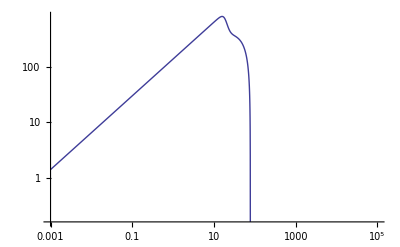

```mathematica
LogLogPlot[growthrate[w],{w,we,10^5}]
```

```mathematica
Max[growthrate]
```

growthrate

```mathematica
growthrate[we]
```

1.39469

```mathematica
growthrate[0.5776841]
```

96.74

```mathematica
mort[w_]:=NIntegrate[(1-fbar)*kappa*(ww^(-lambda))*s[w,ww]*gamma*ww^q,{ww,0,Infinity}]
```

```mathematica
alphaP=(1-fbar)*Sqrt[2*Pi]*kappa*gamma*sigma*(beta^(1+q-lambda))*Exp[sigma*sigma*((1+q-lambda)^2)/2]
```

92.6069

NIntegrate::inumr: The integrand 120.088\ ⅇ^-0.295858\ Log[100\ w/ww]^2/ww^1.33333 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ww near {ww} = {4.81037×10^7}. NIntegrate obtained 27.8321  - 48.2016\ ⅈ
 and 0.104689 for the integral and error estimates.

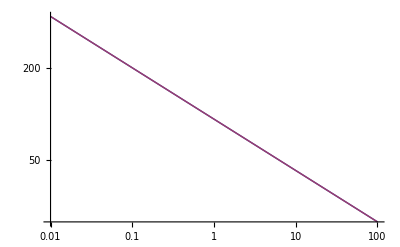

```mathematica
LogLogPlot[{alphaP*w^(n-1),mort[w]},{w,0.01,100}]
```

```mathematica
mort[10]
```

42.9843

```mathematica
alphaP*10^(n-1)
```

42.9843

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ww near {ww} = {2.07884×10^-8}. NIntegrate obtained 4.40367 and 0.0391823 for the integral and error estimates.

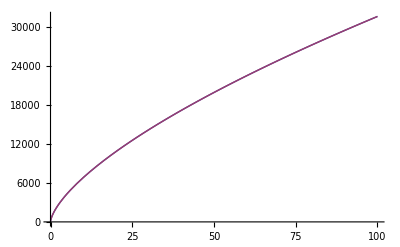

3670.25

```mathematica
Plot[{Ee[w],alphaE*kappa*w^n},{w,0.01,100}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ww near {ww} = {2.07884×10^-8}. NIntegrate obtained 4.40367 and 0.0391823 for the integral and error estimates.

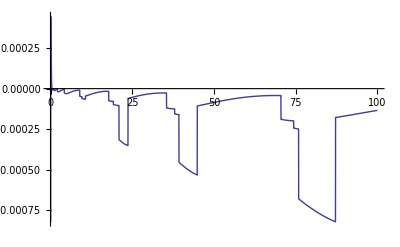

```mathematica
Plot[Ee[w]-alphaE*kappa*w^n,{w,0.01,100}]
```

```mathematica
psi[24.33404,matsize]
```

0.617286

```mathematica
(* agrees with R)
```

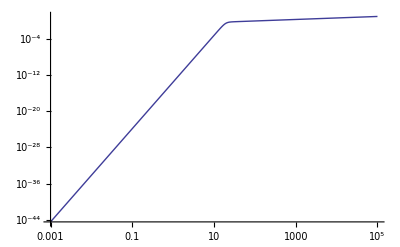

```mathematica
LogLogPlot[psi[w,matsize],{w,we,10^5}]
```

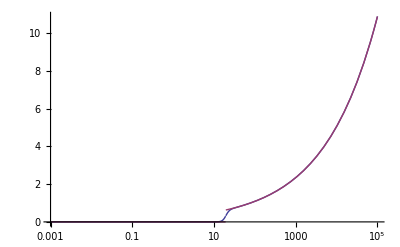

```mathematica
LogLinearPlot[{psi[w,matsize],psi2[w,matsize]},{w,we,10^5}]
```

```mathematica
psi[100,matsize]
```

1.08902

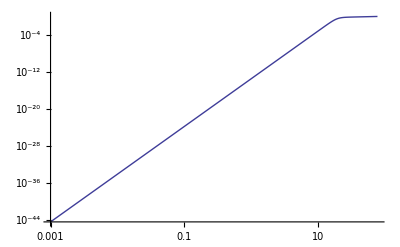

```mathematica
LogLogPlot[psi[w,matsize],{w,we,matsize/eta}]
```

```mathematica
psi[1,matsize]
```

3.17747×10^-14

```mathematica
psi[2.579289,matsize]
```

5.6787×10^-10

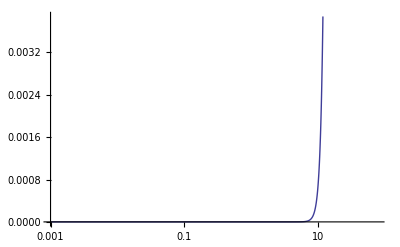

```mathematica
LogLinearPlot[psi[w,matsize],{w,we,matsize/eta}]
```

```mathematica
psi[matsize/eta,matsize]
```

0.999999